```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/kirscher/kette_repo/limit_cycles/src_mathematica/Ganesh

```mathematica
hbar=197.327053;
Mm=938.858;
m1=2 Mm;m2=2 Mm;
μ=m1 m2/(m1+m2);
mh2=(2 μ)/(hbar)^2;
Print["ℏ^2/(2  μ) = ",1/mh2]
```

ℏ^2/(2  μ) = 20.7369

Read LEC list (e.g. fitted to two-body scattering length via <<<Fit_Scattering_length.nb>>>)

```mathematica
(* Nuclear E2=2.22 E3=8.48 ℏc=198*)
(* λ a0,r0 (Martin, 23) a1,r1 (Martin,45) a0 (Rimas, unprojected, 6) a1 (Rimas, unprojected, 7) a0 (Rimas, projected, 8) a1 (Rimas, projected, 9)*)
(*LECsNUCL=Import["../LECs_nucl_Rimas-Martin.dat","Table"];
activeLEC=LECsNUCL[[All,{1,2}]][[2;;]];*)
activeLEC=Import["./tmp.dat","Table"];
```

Calculate the dimer wave function in a Gaussian basis rdimer=∑_(i=1)^N c_i·e^(-α_i r^2)

```mathematica
I1=Compile[{lam,b1,b2},(Pi/(2b1+2b2+lam^2))^(3/2)];
I3=Compile[{b1,b2},3 b1 b2 Pi^(3/2)/(2^(1/2)(b1+b2)^(5/2))];
```

```mathematica
ham=Compile[{lam,b1,b2,lec},Module[{locall=lam},lec I1[lam,b1,b2]+(1/mh2) I3[b1,b2]]];
norm=Compile[{b1,b2},Module[{},(Pi/(2 b1+2 b2))^(3/2)]];
```

```mathematica
ApproxDimerWF[lamd_,dimD_,nbrThreads_,nbrWidthSamples_,minW_,maxW_,minWidthDiff_,verbosity_,σw_:2]:=Block[{LECc,e0,λ=lamd,Δ=minWidthDiff,αmax=maxW,αmin=minW,Nd=dimD,Ns=nbrWidthSamples,Nth=nbrThreads},

LECc=Flatten[Select[activeLEC,#[[1]]==λ&]][[2]];
Print[LECc];
widths={};
rndPrec=5;
Do[

widthLr=Sort[#]&/@RandomReal[{SetPrecision[αmin,rndPrec+1],SetPrecision[αmax,rndPrec+1]},{Ns,Nd},WorkingPrecision->rndPrec];

(*t1=Sort[#]&/@Abs[RandomVariate[NormalDistribution[αmin,σw],{Ns,IntegerPart[Nd/2]}]];
t2=Sort[#]&/@Abs[RandomVariate[NormalDistribution[αmax,σw],{Ns,IntegerPart[Nd/2]}]];

widthLr=ArrayReshape[Flatten[#]&/@Tuples[{t1,t2}],{Nd,Ns}];*)

widthL=Select[widthLr,AllTrue[Select[Tuples[#,2],#[[1]]!=#[[2]]&],Abs[#[[1]]-#[[2]]]>Δ&]&];

AppendTo[widths,widthL];
,{nn,Nth}];

If[verbosity==1,Print["λ = ",λ,"   C_0(λ) = ",LECc,"  #(width-set candidates) = ",Length[Flatten[widths,1]],"  in ",Nth," parallel threads."]];
opti={};
SetSharedVariable[opti];

ta=AbsoluteTime[];
ParallelDo[
widthL=widths[[nt]];
results=0.0;e0=0.0;
optSet={};
Do[
Nd=Length[wi];
hamm=Table[ham[λ,wi[[i]],wi[[j]],LECc],{i,Nd},{j,Nd}];
normm=Table[norm[wi[[i]],wi[[j]]],{i,Nd},{j,Nd}];

{eval,evec}=Eigensystem[{hamm,normm}];

ord=Ordering[Re[eval]];
eigsorted=Re[eval[[ord]]];
vecsorted=evec[[ord]];

If[(
(eigsorted[[1]]<results)&&
(eigsorted[[1]]>-2.65)&&
(Im[eigsorted[[1]]]==0)&&
(NormTF[Transpose[{vecsorted[[1]],wi}]]>10^-5)&&
(Min[Abs[vecsorted[[1]]]]>10^-2)&&
(ContainsOnly[Sign[vecsorted[[1]]],{1}]||ContainsOnly[Sign[vecsorted[[1]]],{-1}])
),
(*Print[eigsorted[[1]],eigsorted];*)
e0=eigsorted[[1]];
results=eigsorted[[1]];
optSet=Transpose[{vecsorted[[1]],wi}];
]
,{wi,widthL}];
If[verbosity==1,Print["Core ",nt," : ",e0,optSet]];
AppendTo[opti,{e0,optSet}];
,{nt,Nth}];
tb=AbsoluteTime[];

e0=Sort[opti][[1]][[1]];
optSet=Sort[opti][[1]][[2]];
If[verbosity==1,Print["optimum of ",Style[Length[Flatten[widths,1]],Red,Italic,18]," candidate width sets found in Δt = ",Style[tb-ta,Red,Italic,18]," sec.          : E_0 = ",e0]];
(*Print["opt. basis: ",optSet];*)
(*Put[optSet,"dimerWF_"<>ToString[e0]<>".mmo"];
Put[e0,"E0_"<>ToString[e0]<>".mmo"];*)
{e0,optSet}
];
rma=2;rmi=0.;nR=100;
rR=Range[rmi,rma,(rma-rmi)/nR];
```

```mathematica
RiccatiBesselJ=Compile[{z,l},z SphericalBesselJ[l,z]];
RiccatiBesselN=Compile[{z,l},(-1)^l z SphericalBesselY[l,z]];
```

```mathematica
(*Boundery conditions for the wavefunction*)
alpha=Compile[{ra,ka,la,ha},RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]];

beta=Compile[{rb,kb,lb,hb},RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])];
```

reference: J. Spanier, K.B. Oldham - An Atlas of Functions (1987)

x·j_n(x)=√((π x)/2)J_(n+1/2)(x)=^(x∈C)√((π x)/2)i^(n+1/2) I_(n+1/2)(Re[x])
with
 j_n: spherical Bessel (1st kind)
 J_n: Bessel (1st kind)
 I_n: modified Bessel (1st kind)
 to optimize runtime, we substitute in this implementation -- valid for S-wave scattering, only:
 j_0(i x)=Sinh[x]/x
 and
 j_1(i x)=i x^-1(Cosh[x]-Sinh[x]/x)
 For numerical stability at arguments x>>1, it is curucial to subsitute the following representation:
 e^(-aR^2-bR'^2) Sinh[bRR']=1/2(e^(-aR^2-bR'^2+bRR')-e^(-aR^2-bR'^2-bRR')) and similarly for the hyperbolic cosine;
 Retaining the Sinh built-in function throws, at best, warnings, and yields significantly inaccurate and almost certainly non-sensical results!

```mathematica
NormTF=Compile[{{core,_Real,2}},(Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]] Gamma[3/2]/(2 (core[[i]][[2]]+core[[j]][[2]])^(3/2)),{i,Length[core]},{j,Length[core]}]]])^2];

VlocTF=Compile[{r,lam,Cc,Dd,Aa,Bb,Gg,Hh,no},Block[{eta2,eta3,w2,w3},
eta2= (8/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5 Cc/(4((1/4)lam^2 Bb + Aa((1/4)lam^2 + 2Gg +2  Bb) + (1/4)lam^2Hh +2 Bb Hh+Gg((1/4)lam^2 +2Hh))^(3/2));
w2= 2(1/4)lam^2(Aa+Hh)(Gg+Bb)/((1/4)lam^2 Bb + Aa((1/4)lam^2+2 Gg+2Bb)+(1/4)lam^2 Hh +2 Bb Hh+Gg((1/4)lam^2+2Hh));
eta3 =(8/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5 Cc/(4((1/4)lam^2 Bb + Gg((1/4)lam^2 + 2Bb)+(1/4)lam^2Hh +2Bb Hh + Aa((1/4)lam^2+2Gg+2Hh))^(3/2));
w3 = 2(1/4)lam^2(Aa+Bb)(Gg+Hh)/((1/4)lam^2 Bb + Gg((1/4)lam^2+2Bb)+(1/4)lam^2 Hh +2Bb Hh+Aa((1/4)lam^2+2Gg+2Hh));
eta2 Exp[-w2 r^2]+eta3 Exp[-w3 r^2]
(*Cc Exp[-lam^2/4 r^2] no*)
]];
```

```mathematica
SolveSecularP3[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},
hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];

normsqu=NormTF[a00];

(*Wmat=ConstantArray[0,{Npoints,Npoints}];*)

Wmats={};
SetSharedVariable[Wmats];

Do[

cij=a00[[ii]][[1]] a00[[jj]][[1]] a00[[kk]][[1]]  a00[[ll]][[1]] normsqu^-1;

amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]],1.],{i,1,Npoints}]];

AppendTo[Wmats,cij amat];

,{ii,1,Length[a00]},{jj,1,Length[a00]},{kk,1,Length[a00]},{ll,1,Length[a00]}];

Wmat=Total[Wmats];
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Amat=Kmat+Dmat+Wmat;

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum  Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);
tanDelta
];
```

```mathematica
GetEREP3[l_,rMax_,nPoints_,core_,LECc_,energ_:0.001]:=Module[{locall=l},
LECd=0.0;
momFM=Sqrt[mh2 energ];
TanDelSwave=SolveSecularP3[rMax,nPoints,momFM,0,locall,LECc,LECd,core,mh2];
-Re[TanDelSwave]/Sqrt[mh2 energ ]
]
```

```mathematica
dCores={{-2.08286,{{-0.0698831, 0.071760}, {-0.227762, 0.48182}, {-0.534198,3.0238}, {-0.811094, 13.460}}},
{-2.03348,{{-0.103955, 0.10433}, {-0.276241, 0.70890}, {-0.610444,3.9917}, {-0.735012, 16.055}}},
{-2.05877,{{-0.107951, 0.10108}, {-0.277921, 0.69288}, {-0.571931,3.5121}, {-0.757815, 13.787}, {-0.098584, 22.437}}},
{-2.05122,{{-0.0668923, 0.055875}, {-0.258185, 0.52526}, {-0.484909,2.8672}, {-0.0737611, 6.5017}, {-0.829632, 13.273}}}};
```

```mathematica
wis=dCores[[All,2]][[All,All,2]]
cos=dCores[[All,2]][[All,All,1]]
dCs=Transpose[{cos[[#]],wis[[#]]}]
```

{{0.07176,0.48182,3.0238,13.46},{0.10433,0.7089,3.9917,16.055},{0.10108,0.69288,3.5121,13.787,22.437},{0.055875,0.52526,2.8672,6.5017,13.273}}

{{-0.0698831,-0.227762,-0.534198,-0.811094},{-0.103955,-0.276241,-0.610444,-0.735012},{-0.107951,-0.277921,-0.571931,-0.757815,-0.098584},{-0.0668923,-0.258185,-0.484909,-0.0737611,-0.829632}}

{{-0.0698831,0.07176},{-0.227762,0.48182},{-0.534198,3.0238},{-0.811094,13.46}}

```mathematica
λ=6;
wi=dCores[[1]][[2]][[All,2]];
Nd=Length[wi];
hamm=Table[ham[λ,wi[[i]],wi[[j]],LECc],{i,Nd},{j,Nd}];
normm=Table[norm[wi[[i]],wi[[j]]],{i,Nd},{j,Nd}];
Print[" = ",hamm//MatrixForm,"              = ",normm//MatrixForm,"\n now transform to a unit-norm basis:"];

{evaln,evecn}=Eigensystem[normm];

diagev=DiagonalMatrix[evaln^(-0.5)];
fulltrafo=Transpose[evecn].diagev;

{evalg,evecg}=Eigensystem[{hamm,normm}];
{eval,evec}=Eigensystem[Transpose[fulltrafo].hamm.fulltrafo];

ord=Ordering[Re[evalg]];
eigsortedg=Re[evalg[[ord]]]
evecsg=evecg[[ord]]//MatrixForm
Norm[evecsg[[1]][[1]]]

ord=Ordering[Re[eval]];
eigsorted=Re[eval[[ord]]]
evecs=evec[[ord]]//MatrixForm
Norm[evecs[[1]][[1]]]

dCoresB=
```

= (133.856 | 10.2732 | -19.011 | -11.7771
10.2732 | 36.3775 | -6.02304 | -9.70678
-19.011 | -6.02304 | 6.69104 | -1.56769
-11.7771 | -9.70678 | -1.56769 | 4.66969)              = (36.2086 | 4.77979 | 0.361469 | 0.0395502
4.77979 | 2.08117 | 0.299939 | 0.0378182
0.361469 | 0.299939 | 0.132375 | 0.0294167
0.0395502 | 0.0378182 | 0.0294167 | 0.0140951)
 now transform to a unit-norm basis:

{-2.09541,11.0702,112.306,840.578}

(-0.0696889 | -0.227721 | -0.534147 | -0.811156
0.142566 | -0.436526 | -0.433592 | -0.775318
0.0194187 | -0.257681 | 0.898433 | 0.355023
-0.00163075 | 0.0256298 | -0.298139 | 0.954177)

1.

{-2.09541,11.0702,112.306,840.578}

(0.819682 | 0.505622 | -0.26157 | 0.0636328
0.562016 | -0.800527 | 0.198838 | -0.0612941
-0.10961 | -0.312739 | -0.943294 | 0.0194278
-0.015645 | -0.0754754 | 0.0473522 | 0.9959)

1.

Obtain dimer-dimer scattering length for the core ensemble

```mathematica
lambdaTest=6;
(* energy at which the scattering length is obtained from the amplitude *)
energ=0.01;
(* Integration grid *)
rMa=4;
grdPerFermi=80;
nGrd=IntegerPart[rMa grdPerFermi];
results={};

nbrOfCores=Length[dCores];
Print["core  λ   LEC      R_max   N # points    E_match    B_dimer      Basis Dim.    a_dd"];
Do[
{e0Core,dimerCore}=dCores[[nn]];

dimCore=Length[dimerCore];

LECc=Flatten[Select[activeLEC,#[[1]]==lambdaTest&]][[2]];
tmp=GetEREP3[lambdaTest,rMa,nGrd,dimerCore,LECc,energ];
AppendTo[results,{lambdaTest,LECc,rMa,nGrd,e0Core,dimCore,tmp,tmp/(hbar/√(Mm Abs[e0Core]))}];
Print[nn,")    ",lambdaTest,"   ",LECc,"   ",rMa,"    ",nGrd,"           ",energ,"     ",e0Core,"   ",dimCore,"             ",tmp];
,{nn,Length[dCores]}];
```

core  λ   LEC      R_max   N # points    E_match    B_dimer      Basis Dim.    a_dd

1)    6   -1090.8   4    320           0.01     -2.08286   4             3.92973

2)    6   -1090.8   4    320           0.01     -2.03348   4             -4.50267

3)    6   -1090.8   4    320           0.01     -2.05877   5             0.0858175

4)    6   -1090.8   4    320           0.01     -2.05122   5             -7.35356

Results core 1 :   a_dd = -12.7977

Results core 2 :   a_dd = -12.7977

Results core 3 :   a_dd = 1.73312

Results core 4 :   a_dd = 1.73312

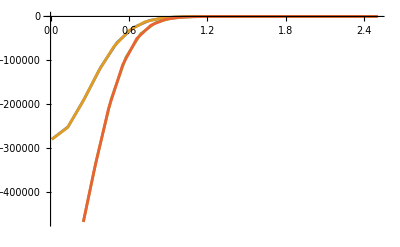

```mathematica
energ=0.01;

(* Integration grid *)
rMa=2.5;
grdPerFermi=29;
nGrd=IntegerPart[rMa grdPerFermi];
LECc=Flatten[Select[activeLEC,#[[1]]==lambdaTest&]][[2]];
(* Plot parameters for the visualization of V(r,r') *)
nR=20;rMi=0.01;thresh=10^-0;

pots={};
Do[
{e0Core,dimerCore}=dCores[[nn]];(*ApproxDimerWF[lambd,dimDimer,nparallelThreads,nDimerWidthSamples,minDimerWidth,maxDimerWidth,midWidthdiff,0];*)

normCore=NormTF[dimerCore];
dimCore=Length[dimerCore];


tmp=GetEREP3[lambdaTest,rMa,nGrd,dimerCore,LECc,energ];
Print["Results core ",nn," :   a_dd = "<>ToString[tmp]];

rR=Range[rMi,rMa,(rMa-rMi)/nR];
nR=Length[rR];
potloc={};
Do[
cij=(*dimerCore[[ii]][[1]] dimerCore[[jj]][[1]] dimerCore[[kk]][[1]]  dimerCore[[ll]][[1]]  *)normCore;
potloctmp=
Table[{rR[[i]],cij VlocTF[rR[[i]],2 lambdaTest^0.5,LECc,0.0,dimerCore[[ii]][[2]],dimerCore[[jj]][[2]],dimerCore[[kk]][[2]],dimerCore[[ll]][[2]],1/normCore]}
,{i,Length[rR]}];
AppendTo[potloc,potloctmp]
,{ii,1,dimCore},{jj,1,dimCore},{kk,1,dimCore},{ll,1,dimCore}];

AppendTo[pots,Transpose[{potloc[[1]][[All,1]],Total[potloc[[All,All,2]]]}]];

,{nn,Length[dCores]}];
ListPlot[pots,Joined->True]
```

### maximal-integration-range dependence of the a_dd scattering-length pre/post-diction

finite-difference runtime Δt = 0.0053777 mins

λ = 6   C_0(λ) = -1090.8     R_max = 6.2     #(grid points) = 192                a_dd = -2.23456 fm        a_dd/a_aa = -0.494795

finite-difference runtime Δt = 0.00789087 mins

λ = 6   C_0(λ) = -1090.8     R_max = 12.25     #(grid points) = 379                a_dd = -2.37021 fm        a_dd/a_aa = -0.524832

finite-difference runtime Δt = 0.013689 mins

λ = 6   C_0(λ) = -1090.8     R_max = 18.3     #(grid points) = 567                a_dd = -2.16355 fm        a_dd/a_aa = -0.479071

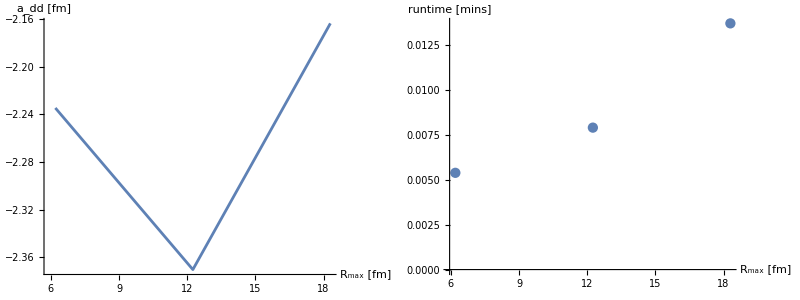

```mathematica
rMaxStart=6.2;
rMaxEnd=18.3;
nbrR=2;

RmaxRange=Range[rMaxStart,rMaxEnd,N[(rMaxEnd-rMaxStart)/nbrR]];
energ=0.001;
grdPerFermi=31;
results={};
runtimes={};
(*SetSharedVariable[results,resultsPhases];*)
Do[
nGrd=IntegerPart[rMa grdPerFermi];
ta=AbsoluteTime[];
tmp=GetEREP3[lambdaTest,rMa,nGrd,dimerCore,LECc,energ];
tb=AbsoluteTime[];
AppendTo[results,tmp];
AppendTo[runtimes,{rMa,(tb-ta)/60.}];
Print["λ = ",lambdaTest,"   C_0(λ) = ",LECc,"     R_max = ",rMa,"     #(grid points) = ",nGrd,"                a_dd = ",tmp," fm        a_dd/a_aa = ",Style[tmp/(hbar/√(Mm Abs[e0Core])),Red,18]];
,{rMa,RmaxRange}]

Grid[{{ListPlot[Transpose[{RmaxRange,results}],ImageSize->Large,Joined->True,AxesLabel->{"R_max [fm]","a_dd [fm]"}],ListPlot[runtimes,ImageSize->Large,AxesLabel->{"R_max [fm]","runtime [mins]"}]}}]
```

```mathematica
0
```

Visualization`Core`ListPlot3D::arrayerr: -- Message text not found -- (Re[4.→0.593595])

Visualization`Core`ListPlot3D::arrayerr: -- Message text not found -- (Re[4.→0.517231])

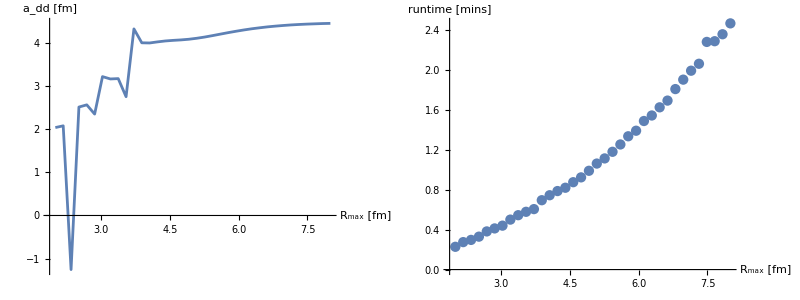

Part::partd: Part specification data⟦4⟧ is longer than depth of object.

Visualization`Core`ListPlot3D::arrayerr: -- Message text not found -- (Re[data⟦4⟧])

Part::partd: Part specification data[[4]] is longer than depth of object.

Visualization`Core`ListPlot3D::arrayerr: 
   -- Message text not found -- (Re[data[[4]]])

Part::partd: Part specification data[[4]] is longer than depth of object.

Visualization`Core`ListPlot3D::arrayerr: 
   -- Message text not found -- (Re[data[[4]]])

Part::partw: Part 4 of {1→0.27913,2→0.383445} does not exist.

Part::partw: Part 4 of {1.→0.27913,2.→0.383445} does not exist.

Visualization`Core`ListPlot3D::arrayerr: -- Message text not found -- (Re[{1.→0.27913,2.→0.383445}⟦4⟧])

Part::partd: Part specification data⟦4⟧ is longer than depth of object.

Visualization`Core`ListPlot3D::arrayerr: -- Message text not found -- (Re[data⟦4⟧])

Part::partd: Part specification data⟦4⟧ is longer than depth of object.

Visualization`Core`ListPlot3D::arrayerr: -- Message text not found -- (Re[data⟦4⟧])

Part::partd: Part specification data⟦4⟧ is longer than depth of object.

Visualization`Core`ListPlot3D::arrayerr: -- Message text not found -- (Re[data⟦4⟧])

Part::partd: Part specification data[[4]] is longer than depth of object.

Visualization`Core`ListPlot3D::arrayerr: 
   -- Message text not found -- (Re[data[[4]]])

```mathematica
lamds={6,10,14,18};
data=Get["nonlocPot_"<>ToString[#]<>".dat"]&/@lamds;
Manipulate[ListPlot3D[Re[data[[n]]],PlotRange->All],{n,Range[1,Length[lamds],1]}]
```

### Grid - density dependence of the a_dd scattering-length pre/post-diction

```mathematica
nGrdi=3;
nGrdiMi=15;
nGrdiMa=252+nGrdiMi;
nGr=Range[nGrdiMi,nGrdiMa,Quotient[nGrdiMa-nGrdiMi,nGrdi]];

results={};
runtimes={};
(*SetSharedVariable[results,resultsPhases];*)
Do[
Print["λ = ",lamd,"   C_0(λ) = ",LECc,"     R_max = ",rMa,"     #(grid points) = ",nGrd];
ta=AbsoluteTime[];
tmp=GetEREP3[lamd,rMa,nGrd,dimerCore,LECc,energ];
tb=AbsoluteTime[];
AppendTo[results,tmp];
AppendTo[runtimes,{nGrd,tb-ta}];
Print["a_dd = ",tmp," fm"];
,{nGrd,nGr}]

Grid[{{ListPlot[Transpose[{nGr,results}],ImageSize->Large,Joined->True,AxesLabel->{"#(grid points)","a_dd [fm]"}],ListPlot[Transpose[{nGr,tt}],ImageSize->Large,AxesLabel->{"#(grid points)","runtime [s]"}]}}]
```

λ = 6   C_0(λ) = -1090.55     R_max = 8     #(grid points) = 15

finite-difference runtime Δt = 0.197998 mins

a_dd = 4.96257 fm

λ = 6   C_0(λ) = -1090.55     R_max = 8     #(grid points) = 99

finite-difference runtime Δt = 1.97576 mins

a_dd = 4.95642 fm

λ = 6   C_0(λ) = -1090.55     R_max = 8     #(grid points) = 183

finite-difference runtime Δt = 6.465 mins

a_dd = 5.05838 fm

λ = 6   C_0(λ) = -1090.55     R_max = 8     #(grid points) = 267

```mathematica
results
aasy=results[[-1]]
Print["a_dd/a =",aasy/(hbar/√(Mm Abs[e0Core]))]
```

{3.92438,3.2987,5.27317,4.55745,4.26782,4.2665,4.40619,4.53118,4.61594,4.6741,4.71599}

4.71599

a_dd/a =0.878303